```mathematica
urn=ParametricPlot3D[{(4+Cos[π h / 25])Cos[t],(4+Cos[π h / 25])Sin[t],h},{h,0,100},{t,0,2π},Boxed->False,Axes->{False,False,True},BoxRatios->{1, 1, 2},PlotPoints->100,PlotTheme->"Monochrome",AxesLabel->{None,None,"cm"},Mesh->25,AxesStyle->Directive["Label",15,Thick]]
```

-Graphics3D-

```mathematica
rurn=Rasterize[Show[urn,ViewPoint->{1.3,-2.4,1.2}]]
Export["/home/merlin/Documents/LaTeX/APPM 1360 Recitation/HW_Fall_2022/HW04/images/Urn.png",Rasterize[Show[rurn,ViewPoint->{1.3,-2.4,1.2}]]]
```

-Graphics-

/home/merlin/Documents/LaTeX/APPM 1360 Recitation/HW_Fall_2022/HW04/images/Urn.png

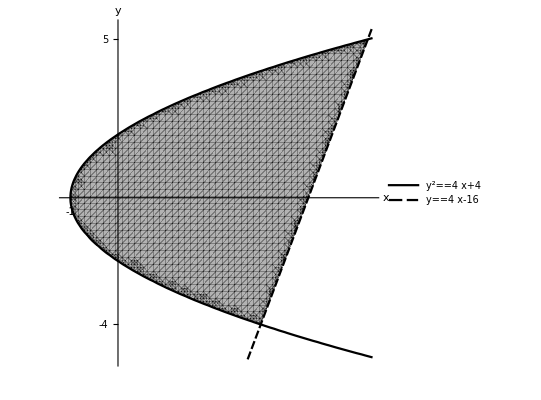

```mathematica
reg=Show[
RegionPlot[(y^2-4)/4<x<(y+16)/4,{x,-1.1,(16+5)/4+0.1},{y,-5.1,5.4},
PlotPoints->50,
PlotTheme->"Monochrome",
BoundaryStyle->None,
Frame->False,
Axes->True,
Ticks->{{-1},{-4,5}},
TicksStyle->Directive["Label", 15,Thick],
AxesLabel->Automatic,
AxesStyle->Directive["Label",15,Thick]],
ContourPlot[{y^2==4x+4,y==4x-16},{x,-1.1,(16+5)/4+0.1},{y,-5.1,5.4},
PlotLegends->"Expressions",
LabelStyle->Directive["Label", 25],
PlotTheme->"Monochrome"]]
```

```mathematica
Export["/home/merlin/Documents/LaTeX/APPM 1360 Recitation/HW_Fall_2022/HW04/images/Region.png",reg]
```

/home/merlin/Documents/LaTeX/APPM 1360 Recitation/HW_Fall_2022/HW04/images/Region.png

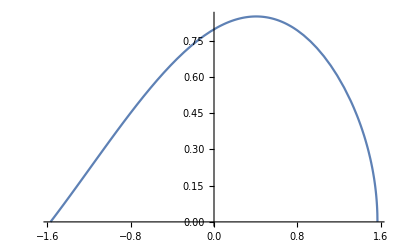

```mathematica
Plot[Cos[x]/(√(π/2-x)),{x,-π/2,π/2}]
```

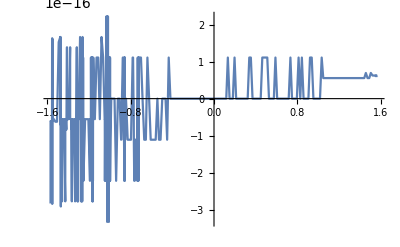

```mathematica
Plot[{Cos[x]-Sin[π/2-x]},{x,-π/2,π/2},PlotPoints->200]
```

```mathematica
V[h_]=∫_-8^(-8+h) π(64-y^2)ⅆy
Solve[V[h]==500,h,Reals]//N
```

8 h^2 π-(h^3 π)/3

{{h→-4.12058},{h→5.01493},{h→23.1057}}

```mathematica
∫_0^100 π(4+Cos[π h/25])^2 ⅆh
∫_0^100 π(3+Cos[π h/25])^2 ⅆh
```

1650 π

950 π